## Interpolation with Newton Divided Difference and Lagrange Polynomials Jacob Russell

```mathematica
(* Modules *)
```

```mathematica
lagrange[dataPoints_,x_]:=Module[{n = Length[dataPoints]},
Return[∑_(j=1)^n (dataPoints⟦j,2⟧*(∏_(k=1)^(j-1) (x - dataPoints⟦k,1⟧)/(dataPoints⟦j,1⟧-dataPoints⟦k,1⟧))*(∏_(k=j+1)^n (x - dataPoints⟦k,1⟧)/(dataPoints⟦j,1⟧-dataPoints⟦k,1⟧)))];
]
```

```mathematica
dividedDifference[XY_,x_]:=Module[{X=XY⟦All,1⟧, Y=XY⟦All,2⟧,n,ddTable},
n = Length[X];
ddTable = Table[0,{n},{n}];
ddTable⟦All,1⟧=Y⟦All⟧;
Do[ddTable⟦k,j⟧=(ddTable⟦k,j-1⟧-ddTable⟦k-1,j-1⟧)/(X⟦k⟧-X⟦k-j+1⟧),{j,2,n},{k,j,n}];
Return[∑_(t=1)^n ddTable⟦t,t⟧*∏_(i=1)^(t-1) (x-X⟦i⟧)]
]
```

## 1) Interpolate through the following points using the Lagrange Interpolating Polynomial.

```mathematica
(* Define given points *)
```

```mathematica
interpolatingPoints = List[{1.,0.},{2.,1.88416938536372},{3.,4.9236386866629545},{4.,10.243406803946097},{5.,19.60696764835563},{6.,35.98845097665124},{7.,64.43969405697302},{8.,113.53366127778843}];
```

```mathematica
(* Interpolating using Lagrange *)
```

```mathematica
lagrange[interpolatingPoints,x]
```

0.+0.0026169 (-8.+x) (-7.+x) (-6.+x) (-5.+x) (-4.+x) (-3.+x) (-1.+x)-0.0205152 (-8.+x) (-7.+x) (-6.+x) (-5.+x) (-4.+x) (-2.+x) (-1.+x)+0.0711348 (-8.+x) (-7.+x) (-6.+x) (-5.+x) (-3.+x) (-2.+x) (-1.+x)-0.136159 (-8.+x) (-7.+x) (-6.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x)+0.149952 (-8.+x) (-7.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x)-0.0894996 (-8.+x) (-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x)+0.0225265 (-7.+x) (-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x)

```mathematica
Simplify[%54]
```

```mathematica
(* Here we see the interpolating polynomial *)
```

-1.774+2.197 x-0.756989 x^2+0.40361 x^3-0.0826691 x^4+0.0141451 x^5-0.0011538 x^6+0.0000558367 x^7

```mathematica
Plot[-1.7740004736093056+2.197001626217798 x-0.7569894935113552 x^2+0.4036102452397472 x^3-0.08266905646030409 x^4+0.014145117639593252 x^5-0.0011538022451864638 x^6+0.000055836728560243465 x^7,{x,1,8}]
```

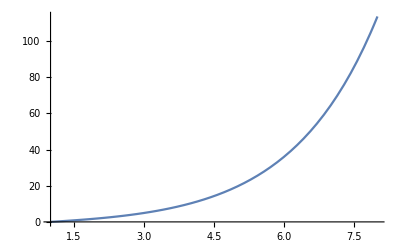

```mathematica
(* Plotting for clarity *)
```

Evaluating the function at x = 110 would not be advisable because we would venture into the realm
of extrapolation, rather than interpolation.

## 2) Given r(x), interpolate r(x) for x=0 to 5 with step size 0.5.

```mathematica
(* Defining given points *)
```

```mathematica
interpolatingPoints2 = Table[{x, Cos[Cos[x]]}, {x,0,5,.5}]
```

{{0.,0.540302},{0.5,0.639012},{1.,0.857553},{1.5,0.997499},{2.,0.914653},{2.5,0.695886},{3.,0.548696},{3.5,0.592646},{4.,0.793873},{4.5,0.977865},{5.,0.960037}}

```mathematica
(* Interpolating using Newton Divided Difference *)
```

```mathematica
dividedDifference[interpolatingPoints2,x]
```

0.540302+0.19742 (0.+x)+0.239661 (-0.5+x) (0.+x)-0.264567 (-1.+x) (-0.5+x) (0.+x)+0.0361522 (-1.5+x) (-1.+x) (-0.5+x) (0.+x)+0.047157 (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)-0.0255357 (-2.5+x) (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)+0.00480376 (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)+0.000330553 (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)-0.000505254 (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)+0.000216867 (-4.5+x) (-4.+x) (-3.5+x) (-3.+x) (-2.5+x) (-2.+x) (-1.5+x) (-1.+x) (-0.5+x) (0.+x)

```mathematica
(* Interpolating polynomial *)
```

```mathematica
Simplify[%16]
```

0.540302-0.107569 x+1.1088 x^2-1.80969 x^3+2.47082 x^4-2.16629 x^5+1.09473 x^6-0.324966 x^7+0.0565938 x^8-0.00538477 x^9+0.000216867 x^10

```mathematica
(* Plotting for clarity *)
```

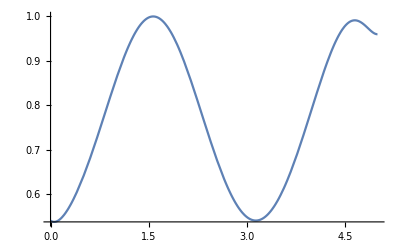

```mathematica
Plot[%75,{x,0,5}]
```

## 3) Application question

```mathematica
(* First, let's instantiate the sum and find the sum of the first n integers *)
f[x_] =∑_(k=1)^x k^5;
```

```mathematica
f[n]
```

1/12 n^2 (1+n)^2 (-1+2 n+2 n^2)

```mathematica
(* Plotting a few points for visualization *)
```

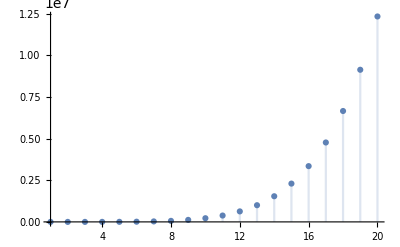

```mathematica
DiscretePlot[1/12 n^2 (1+n)^2 (-1+2 n+2 n^2),{n,1,20}]
```

```mathematica
(* Similarly to the example given, we can derive the function with 7 points because the funciton is of degree 6 *)
```

```mathematica
interpolatingPoints3 = Table[{x, f[x]}, {x,1,7,1}]
```

{{1,1},{2,33},{3,276},{4,1300},{5,4425},{6,12201},{7,29008}}

```mathematica
(* Veryfing using our Newton Divided Difference module *)
dividedDifference[interpolatingPoints3,x]
```

1+32 (-1+x)+211/2 (-2+x) (-1+x)+95 (-3+x) (-2+x) (-1+x)+125/4 (-4+x) (-3+x) (-2+x) (-1+x)+4 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x)+1/6 (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Simplify[1+32 (-1+x)+211/2 (-2+x) (-1+x)+95 (-3+x) (-2+x) (-1+x)+125/4 (-4+x) (-3+x) (-2+x) (-1+x)+4 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x)+1/6 (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x)]
```

```mathematica
(* The interpolating polynomial is the same *)
```

1/12 x^2 (1+x)^2 (-1+2 x+2 x^2)

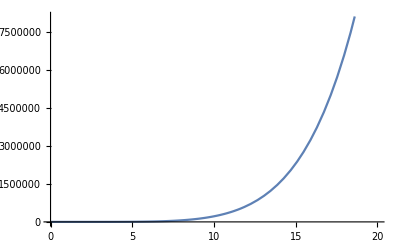

```mathematica
Plot[1/12 x^2 (1+x)^2 (-1+2 x+2 x^2),{x,0,20}]
```

```mathematica
(* Verifying graphically *)
p1=DiscretePlot[1/12 n^2 (1+n)^2 (-1+2 n+2 n^2),{n,0,20}];
p2=Plot[1/12 x^2 (1+x)^2 (-1+2 x+2 x^2),{x,0,20}];
```

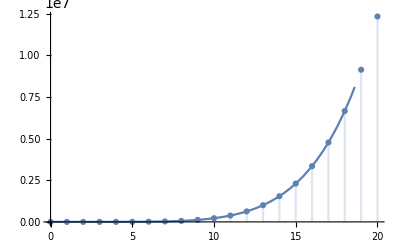

```mathematica
Show[p1,p2]
```